```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];Get["./DefinitionsAndAssumptions.m"];Get["./SetupEnvironment.m"];
ClearVars;Print[ShowVariableDefinitions];
```

Definitions and assumptions for analysis of consumption and portfolio choice with risky and safe assets.

(r0 |  | log riskfree return (rate)
lℛ |  | log expected risky return factor (≠ 𝔼[Log[ℛtp1]])
σ |  | standard deviation of log risky return
ρ |  | relative risk aversion
φ |  | lℛ-r0 = log of the level equity premium (= Log[Φ]≠ 𝔼t[Log[Φtp1]])
ϛ |  | portfolio share in the risky asset)

Variables and formulas derived from the elemental environmental variables.

(R0 |  | Exp[r0] = riskfree return (factor)
ℛtp1 |  | Realized risky return (factor)
ℛ == 𝔼_t[ℛtp1] |  | Expected risky return (factor)
𝓇tp1 == Log[ℛtp1] |  | realized log risky return (rate)
𝓇tp1 | ~ | 𝒩(lℛ - σ^2/2,σ^2) → 𝔼_t[𝓇tp1] = lℛ - σ^2/2
𝓇 | = | 𝔼_t[𝓇tp1]
Φ |  | Expected equity premium (factor)
φ |  | lℛ-r0 = log of the level equity premium (= Log[Φ]≠ 𝔼t[Log[Φtp1]])
ϕtp1 |  | Realized logarithmic equity premium
ϕtp1 | ~ | 𝒩(φ - σ^2/2,σ^2) → {𝔼_t[ϕtp1] = φ - σ^2/2, log 𝔼Φtp1 = φ - σ^2/2 + σ^2/2 = φ} by MathFact LogELogNorm
ϕ  | = | 𝔼_t[ϕtp1] = Expectation of realized logarithmic equity premium
ℜtp1 | == | R0 + (ℛtp1-R0)ϛ  = arithmetic (exactly correct) portfolio return
ℜ | == | 𝔼_t[R0 + (ℛtp1-R0)ϛ] = expected arithmetic (exactly correct) portfolio return
lℜ | == | Log[ℜ] = arithmetic (exactly correct) portfolio return)

Null

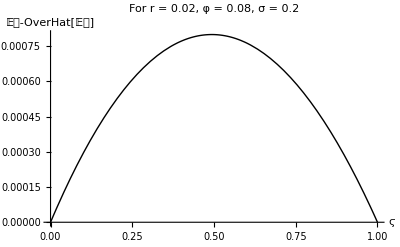

```mathematica
ClearVars;lℛ = r0+φ;σ=0.2;r0=0.02;φ=0.08;
(* First, show that the approximation of the (true) arithmetic return by the Campbell-Viceira approximation
   is good *)
ExactMinusApproxLogExpectedPortfolioReturn = 
Plot[{lℜNInt[ϛ,σ]-lℜCVApprox[ϛ,σ]}
  ,{ϛ,0,1}
  ,AxesLabel->{"ϛ","𝔼𝔯-OverHat[𝔼𝔯]"}
  ,BaseStyle->{FontSize->14}
  ,PlotLabel->"For r = "<>ToString[r0]<>", φ = "<>ToString[φ]<>", σ = "<>ToString[σ]
];
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.pdf",ExactMinusApproxLogExpectedPortfolioReturn];
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.png",ExactMinusApproxLogExpectedPortfolioReturn,ImageSize->72 9];
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.svg",ExactMinusApproxLogExpectedPortfolioReturn];
Print[ExactMinusApproxLogExpectedPortfolioReturn];
```

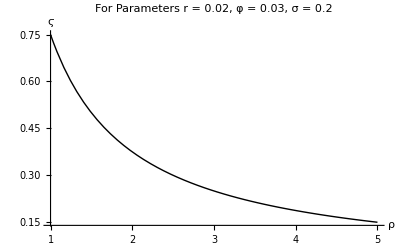

```mathematica
lℛ=0.05;r0=0.02;φ=lℛ-r0;σ=0.2;
ShareVsCRRA = Plot[ϛOptCVApprox[σ,ρ],{ρ,1,5}
,AxesLabel->{"ρ","ϛ"}
,PlotLabel->"For Parameters r = "<>ToString[r0]<>", φ = "<>ToString[φ]<>", σ = "<>ToString[σ]
,BaseStyle->{FontSize->14}
];
Export["./Figures/ShareVsCRRA.pdf",ShareVsCRRA];
Export["./Figures/ShareVsCRRA.png",ShareVsCRRA,ImageSize->72 9];
Export["./Figures/ShareVsCRRA.svg",ShareVsCRRA];
Print[ShareVsCRRA];
```

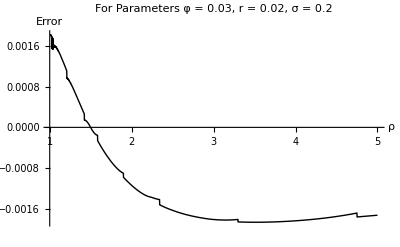

```mathematica
(*Off[NIntegrate::inumr]; (*Turn off some annoying warning messages*)*)
ShareApproxErr=Plot[{ϛOptDirect[σ,ρ]-ϛOptCVApprox[σ,ρ]},{ρ,1.01,5}
,PlotLabel->"For Parameters φ = "<>ToString[φ]<>", r = "<>ToString[r0]<>", σ = "<>ToString[σ]
,BaseStyle->{FontSize->14}
,AxesLabel->{"ρ","Error"}];
Export["./Figures/ShareApproxErr.pdf",ShareApproxErr];
Export["./Figures/ShareApproxErr.png",ShareApproxErr,ImageSize->72 9];
Export["./Figures/ShareApproxErr.svg",ShareApproxErr];
Print[ShareApproxErr];
(*On[NIntegrate::inumr];*)
```

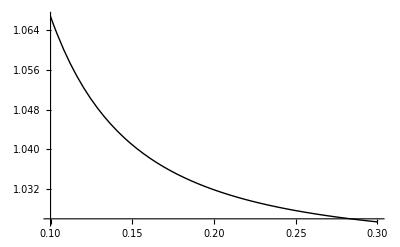

```mathematica
Print[Plot[𝔼ℜGivenOptϛCVApprox[σPlot,ρ=2],{σPlot,0.1,0.3}]];
```

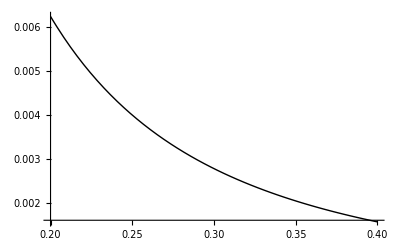

```mathematica
Print[Plot[σ𝔯tp1GivenϛCVApprox[σPlot,3],{σPlot,0.2,0.4}]];
```

```mathematica
𝓇
```

0.03

```mathematica
φ
```

0.03

```mathematica
σ
```

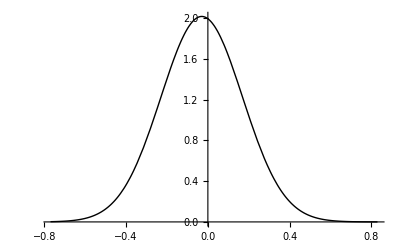

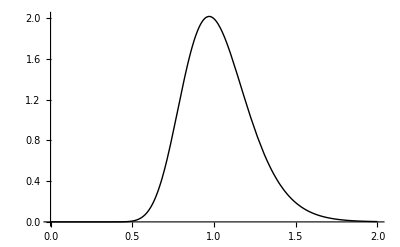

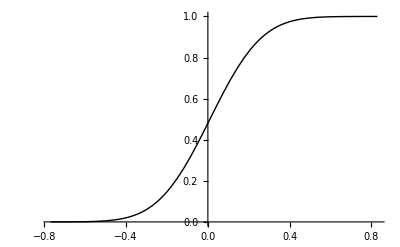

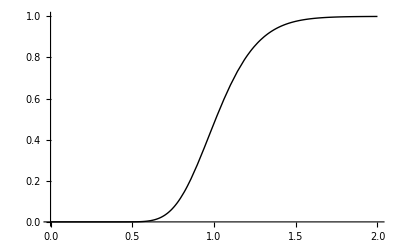

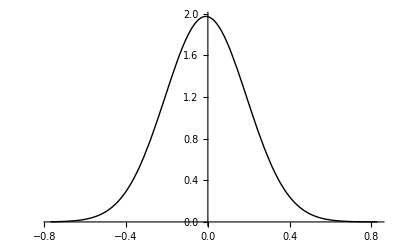

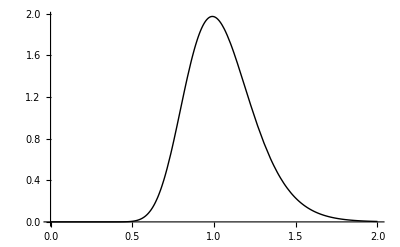

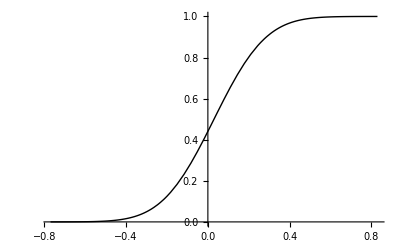

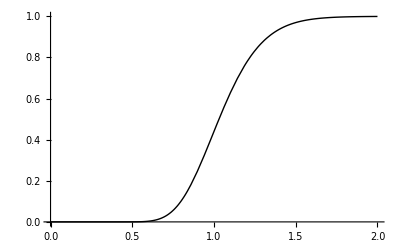

```mathematica
Get["./Extra-Plots.m"];
```